```mathematica
Subscript[k, 0]=20;
Subscript[X, 0]=-5;
Subscript[X, d]=-3;
δ=0.5;
Subscript[δ, 1]=0.005;

n=10;
m=4;
Ti=-0.02;
Tf=0.22;
dt=(Tf-Ti)/(n-1);

tm[0]=Ti-dt;
tm[1]=Ti;
tm[n+1]=Tf+dt;
list={};
Do[tm[i]=tm[i-1]+dt,{i,2,n}];
Do[list=Append[list,tm[i]],{i,1,n}];

ψ[0,x_,t_]:=(δ^2/(2π))^(1/4)*Exp[-Subscript[k, 0]^2*δ^2]/(√(δ^2+(ⅈ*t)/2))*Exp[((2*δ^2* Subscript[k, 0] + ⅈ*(x-Subscript[X, 0]))^2)/(4*δ^2 + 2*ⅈ*t)]
K[xf_,tf_,xi_,ti_]:=1/(√(2*π*ⅈ*(tf-ti)))*Exp[(ⅈ*(xf-xi)^2)/(2*(tf-ti))]

a[1,T1_]=Abs[ψ[0,Subscript[X, d],T1]]*Sqrt[Subscript[δ, 1]];
b[1,T1_]=√(1-(a[1,T1])^2);

α[0,T1_]=ψ[0,Subscript[X, d],T1];

β[i,T_]=Do[K[Subscript[X, d],0,Subscript[X, d],T-TM[i]],{i,1,n}];

Do[α[i,T_]=(α[i-1,T]-α[i-1,TM[i]]*β[i,T]*Subscript[δ, 1])/b[i,T];a[i+1,T_]=Abs[α[i,T]]*Sqrt[Subscript[δ, 1]];b[i+1,T_]=√(1-(a[i+1,T])^2),{i,1,n}];
```

```mathematica
TList=Permutations[list,{m}];
```

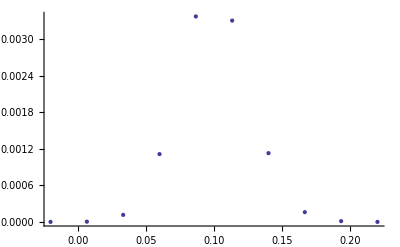

0.100381

```mathematica
Do[prob[i_]:=(∏_(k=1)^(i-1) b[k]^2)*(a[i])^2,{i,2,n,1}]
prob[1]=(a[1])^2;

ListPlot[Table[{tm[i],prob[i]},{i,n}],PlotRange->All]

tbar=(∑_(j=1)^n (tm[j]*prob[j]))/(∑_(j=1)^n prob[j])
```